## General-Purpose Functions

```mathematica
fourPointDataDir=StringDelete[NotebookDirectory[],"Note_Paul"]<>"consolidated_data";
```

```mathematica
SetDirectory[fourPointDataDir];

niceTime[timeInSec_]:=If[timeInSec<($TimeUnit/100)||Not[NumericQ[timeInSec]]||Precision[timeInSec]==0,"",Block[{measure=Select[Transpose[{(Quotient[Mod[timeInSec,#1],#2]&@@@Partition[{timeInSec 10,3.15569277216*^7,3600*24.,3600.,60.,1.,10^-3,10.^-6,10.^-9},2,1]),{" years"," days"," hours"," minutes"," seconds"," ms"," μs"," ns"}}],#[[1]]>0&]},If[Length[measure]>0,Row[Row[#,""]&/@measure[[1;;Min[2,Length[measure]]]],", "],""]]];
map[function_,list_]:=If[Length[list]>0,Module[{monitor=0,len=Length[list],newFcn,t00=AbsoluteTime[]},newFcn[i_]:=(monitor=i;function[list[[i]]]);Monitor[Map[newFcn,Range[len]],(Column[{ProgressIndicator[(monitor-1)/len,ImageSize->{1250,30},ImageMargins->0,BaselinePosition->Center],If[monitor≥1,Row[{If[monitor>1,Row[{niceTime[Round[AbsoluteTime[]-t00]]," so far; approx. ",niceTime[Round[((AbsoluteTime[]-t00)/(monitor-1))*(len-monitor+1)]]," remaining."}],"                                              "]," (",monitor-1,"/",len,")"}],""]},Alignment->Left,Spacings->0.1])]],Map[function,list]];
littleGroup[graph_]:=Block[{num=Numerator[graph],den=Denominator[graph]},num=Join@@(Function[{y,z},y&/@Range[z]]@@@FactorList[num][[2;;-1]]);den=Join@@(Function[{y,z},y&/@Range[z]]@@@FactorList[den][[2;;-1]]);-(Count[num,#,{0,∞}]-Count[den,#,{0,∞}])&/@Sort[DeleteDuplicates[Flatten[List@@@Cases[graph,_x,{0,∞}]]]]];
```

## Basic Data Functions

```mathematica
planarGraphDials[loop_]:=Block[{fileName=FileNameJoin[{fourPointDataDir,(("fGraph_dials_"<>ToString[loop]<>".tex"))}]},If[FileExistsQ[fileName],Set[planarGraphDials[loop],ReadList[fileName]],{{}}]];
planarGraphEdges[loop_]:=Block[{fileName=FileNameJoin[{fourPointDataDir,(("fGraph_edges_"<>ToString[loop]<>".tex"))}],raw,rule},If[FileExistsQ[fileName],(raw=ReadList[fileName];rule=Thread[Rule[Range[Binomial[4+loop,2]],Subsets[Range[4+loop],{2}]]];Set[planarGraphEdges[loop],(raw/.rule)]),{{}}]];
fGraphNums[loop_]:=Block[{fileName=FileNameJoin[{fourPointDataDir,("fGraph_nums_"<>ToString[loop]<>".tex")}],raw,rule},If[FileExistsQ[fileName],(raw=ReadList[fileName];rule=Thread[Rule[Range[Binomial[4+loop,2]],Subsets[Range[4+loop],{2}]]];raw=Times@@@#&/@(x@@@#&/@#&/@(raw/.rule));Set[fGraphNums[loop],raw]),{{}}]];
fGraphList[loop_]:=If[FileExistsQ[FileNameJoin[{fourPointDataDir,("fGraph_nums_"<>ToString[loop]<>".tex")}]],Set[fGraphList[loop],(Join@@(fGraphNums[loop](1/(Times@@@(x@@@#&/@planarGraphEdges[loop])))))],{{}}];

amplitudeCoefficients[loop_]:=Block[{fileName=FileNameJoin[{fourPointDataDir,(("amplitudeCoefficients_"<>ToString[loop]<>".tex"))}]},If[FileExistsQ[fileName],Set[amplitudeCoefficients[loop],(<<(fileName))],{}]];
```

```mathematica
(* This takes you from the fnum list to the dialnumber list position *)
fnumtodialnum[loop_,fnum_]:=Position[Table[Range[#[[i]]+1,#[[i+1]]],{i,1,Length[#]-1}]&@Prepend[Accumulate[Length/@fGraphNums[loop]],0],fnum][[1]]
dialnumtofnum[loop_,{dial_,num_}]:=(Table[Range[#[[i]]+1,#[[i+1]]],{i,1,Length[#]-1}]&@Prepend[Accumulate[Length/@fGraphNums[loop]],0])[[dial,num]]
```

```mathematica
Length/@fGraphNums[6]
```

{3,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,2,1,2,1,1,1,1,1,1,1,1,1,1,1,1}

## Graph Analysis

```mathematica
takeSmallest[x_,p_] := Take[Sort[x],p]
```

```mathematica
graphIsomorphisms[fcnList__]/;(Length[{fcnList}]==2):=Block[{factors={fcnList},isoList,bases,nums,baseLabels=DeleteDuplicates[Cases[{fcnList}[[1]],x[y__]:>y,{0,∞}]]},If[Length[DeleteDuplicates[factors]]==1,((bases=(Function[{q},List@@@DeleteDuplicates[Cases[Denominator[q],x[y__],{0,∞}]]]/@factors);nums=(factors*((Times@@(x@@@#))&/@bases));bases=Graph[UndirectedEdge@@@#]&/@bases;isoList=(FindGraphIsomorphism[#1,#2,All]&@@bases);If[Length[isoList]==0,{},(isoList=(Function[{iso},Thread[Rule@@(baseLabels/.{{},iso})]]/@isoList);isoList=Select[isoList,SameQ[nums[[2]],(nums[[1]]/.{x[y__]:>(x@@Sort[{y}/.#])})]&])])),(Which[Not[SameQ@@(LeafCount/@factors)],{},True,(bases=(Function[{q},List@@@DeleteDuplicates[Cases[Denominator[q],x[y__],{0,∞}]]]/@factors);nums=(factors*((Times@@(x@@@#))&/@bases));bases=Graph[UndirectedEdge@@@#]&/@bases;isoList=(FindGraphIsomorphism[#1,#2,All]&@@bases);If[Length[isoList]==0,{},(isoList=(Function[{iso},Thread[Rule@@(baseLabels/.{{},iso})]]/@isoList);isoList=Select[isoList,SameQ[nums[[2]],(nums[[1]]/.{x[y__]:>(x@@Sort[{y}/.#])})]&])])])]];
graphIsomorphism[fcnList__]/;(Length[{fcnList}]==2):=Block[{factors={fcnList},isoList,bases,nums,baseLabels=DeleteDuplicates[Cases[{fcnList}[[1]],x[y__]:>y,{0,∞}]]},If[Length[DeleteDuplicates[factors]]==1,Thread[Rule[baseLabels,baseLabels]],(Which[Not[SameQ@@(LeafCount/@factors)],{},True,(bases=(Function[{q},List@@@DeleteDuplicates[Cases[Denominator[q],x[y__],{0,∞}]]]/@factors);nums=(factors*((Times@@(x@@@#))&/@bases));bases=Graph[UndirectedEdge@@@#]&/@bases;isoList=(FindGraphIsomorphism[#1,#2,All]&@@bases);If[Length[isoList]==0,{},(isoList=(Function[{iso},Thread[Rule@@(baseLabels/.{{},iso})]]/@isoList);isoList=Select[isoList,SameQ[nums[[2]],(nums[[1]]/.{x[y__]:>(x@@Sort[{y}/.#])})]&,1])])])]];
graphEquivalentQ[fcnList__]/;(Length[{fcnList}]==2):=Not[graphIsomorphism[fcnList]==={}];
distinctGraphs[seedList_]:=DeleteDuplicates[seedList,graphEquivalentQ];
graphAutomorphisms[graph_]:=graphIsomorphisms[graph,graph];
graphSymmetryFactor[graph_]:=Length[graphAutomorphisms[graph]];
canonicalizeGraph[graph_]:=Block[{baseEdges=List@@@DeleteDuplicates[Cases[Denominator[graph],x[y__],{0,∞}]],baseLabels,baseGraph,auto},baseLabels=DeleteDuplicates[Flatten[baseEdges]];baseGraph=Graph[UndirectedEdge@@@baseEdges];auto=(Function[{iso},Thread[Rule@@(baseLabels/.{{},iso})]]/@FindGraphIsomorphism[baseGraph,CanonicalGraph[baseGraph]])[[1]];graph/.{x[q__]:>x@@(Sort[{q}/.auto])}];

orderedVertsToFaces[dialList_]:=Block[{edgeRules,fullEdgeList},edgeRules=Join@@Table[(Rule[{#1,j},{j,#2}]&@@@Partition[dialList[[j]],2,1,1]),{j,Length[dialList]}];fullEdgeList=edgeRules[[All,1]];Sort@DeleteDuplicates[Function[{start},(Function[{term},Sort[Partition[Reverse@term,Length[term],1,1]][[1]]]@DeleteDuplicates[Join@@NestWhile[Append[#,(#[[-1]]/.edgeRules)]&,{start},Length[DeleteDuplicates[#]]==Length[#]&]])]/@fullEdgeList]];
```

```mathematica
degree[fgraph_,v_]:=Count[Denominator[fgraph]/.Times->List/.x->List//Flatten,v]
```

```mathematica
fgraphtograph[fgraph_]:=Graph[(List@@Denominator[fgraph])/.x->List]
```

NB Problem with canonicalise graph . See two examples below . Is it not doing numerators?

New canonicalise: canonicalisefgraph . First canonicalises the denominator using inbuilt mathematica . Then applies the autumorphism group of the resulting graph to the numerator and selects the first in the ordered list . This seems to work...

```mathematica
numeratormonomialtolist[numerator_]:=If[Head[numerator]===Integer,{},ConstantArray@@@Transpose[{Cases[#,x[_,_],Infinity],Exponent[#,Cases[#,x[_,_],Infinity]]}]&@({numerator/.Times->List}//Flatten)//Flatten]
```

```mathematica
canonicalizefgraph[fgraph_]:=Module[{fgraph2,dengraphcan,dengraphtocanisomorphism,dencan,numcan1,numcan,dengraph,numedgelist},fgraph2=fgraph/.x[a_,b_]:>x[b,a]/;(b<a);
dengraph=fgraphtograph[fgraph2];
dengraphcan=CanonicalGraph[dengraph];
dengraphtocanisomorphism=((FindGraphIsomorphism[dengraph,dengraphcan]//Normal)[[1]]);
numedgelist=numeratormonomialtolist[Numerator[fgraph2]];
numcan1=numedgelist/.dengraphtocanisomorphism/.x[a_,b_]:>x[b,a]/;(b<a);
dencan=Times@@(EdgeList[dengraphcan]/.UndirectedEdge->x);
numcan=takeSmallest[Times@@@PermutationReplace[numcan1,GraphAutomorphismGroup[dengraphcan]]/.x[exp__]:>x[Sequence@@Sort[{exp}]]/;(Sort[{exp}]=!={exp}),1][[1]];
numcan/dencan]
```

```mathematica
fGraphList[4];
1/graphSymmetryFactor/@%;
amplitudeCoefficients[4] % %%//Total
```

-1/(16 x[1,5] x[1,6] x[1,7] x[1,8] x[2,3] x[2,4] x[2,7] x[2,8] x[3,4] x[3,6] x[3,8] x[4,5] x[4,7] x[5,6] x[5,7] x[6,8])+(x[5,6] x[7,8])/(8 x[1,4] x[1,6] x[1,7] x[1,8] x[2,3] x[2,5] x[2,6] x[2,8] x[3,5] x[3,6] x[3,7] x[4,5] x[4,7] x[4,8] x[5,7] x[5,8] x[6,7] x[6,8])+x[7,8]^2/(24 x[1,5] x[1,6] x[1,7] x[1,8] x[2,3] x[2,4] x[2,7] x[2,8] x[3,6] x[3,7] x[3,8] x[4,5] x[4,7] x[4,8] x[5,7] x[5,8] x[6,7] x[6,8])

```mathematica
fGraphList[5];
1/graphSymmetryFactor/@%;
amplitudeCoefficients[5] % %%//Total
```

1/(12 x[1,6] x[1,7] x[1,8] x[1,9] x[2,4] x[2,5] x[2,8] x[2,9] x[3,4] x[3,5] x[3,6] x[3,7] x[4,7] x[4,9] x[5,6] x[5,8] x[6,7] x[8,9])+(x[5,9] x[6,9] x[7,8])/(4 x[1,4] x[1,6] x[1,8] x[1,9] x[2,3] x[2,5] x[2,8] x[2,9] x[3,5] x[3,7] x[3,9] x[4,6] x[4,7] x[4,9] x[5,6] x[5,7] x[5,8] x[6,7] x[6,8] x[7,9] x[8,9])+(x[4,6] x[5,8] x[7,9])/(6 x[1,5] x[1,6] x[1,8] x[1,9] x[2,4] x[2,6] x[2,7] x[2,8] x[3,4] x[3,5] x[3,7] x[3,9] x[4,7] x[4,8] x[4,9] x[5,6] x[5,7] x[5,9] x[6,7] x[6,8] x[8,9])-(x[6,8] x[7,9])/(8 x[1,3] x[1,4] x[1,8] x[1,9] x[2,3] x[2,4] x[2,6] x[2,7] x[3,7] x[3,8] x[4,6] x[4,9] x[5,6] x[5,7] x[5,8] x[5,9] x[6,7] x[6,9] x[7,8] x[8,9])-x[8,9]/(2 x[1,2] x[1,3] x[1,4] x[1,9] x[2,3] x[2,4] x[2,8] x[3,6] x[3,9] x[4,5] x[4,8] x[5,7] x[5,8] x[5,9] x[6,7] x[6,8] x[6,9] x[7,8] x[7,9])+(x[6,7] x[8,9]^2)/(4 x[1,2] x[1,6] x[1,7] x[1,9] x[2,6] x[2,7] x[2,8] x[3,4] x[3,5] x[3,8] x[3,9] x[4,7] x[4,8] x[4,9] x[5,6] x[5,8] x[5,9] x[6,8] x[6,9] x[7,8] x[7,9])+x[8,9]^3/(28 x[1,6] x[1,7] x[1,8] x[1,9] x[2,3] x[2,5] x[2,8] x[2,9] x[3,4] x[3,8] x[3,9] x[4,7] x[4,8] x[4,9] x[5,6] x[5,8] x[5,9] x[6,8] x[6,9] x[7,8] x[7,9])

```mathematica
g1=(x[4,9] x[5,6] x[7,8] x[10,11]^2)/(x[1,6] x[1,7] x[1,8] x[1,9] x[2,3] x[2,4] x[2,10] x[2,11] x[3,5] x[3,10] x[3,11] x[4,6] x[4,8] x[4,10] x[4,11] x[5,7] x[5,9] x[5,10] x[5,11] x[6,7] x[6,8] x[6,10] x[7,9] x[7,10] x[8,9] x[8,11] x[9,11]);g2=(x[4,5] x[6,9] x[7,8] x[10,11]^2)/(x[1,4] x[1,5] x[1,6] x[1,7] x[2,3] x[2,9] x[2,10] x[2,11] x[3,8] x[3,10] x[3,11] x[4,6] x[4,7] x[4,9] x[4,11] x[5,6] x[5,7] x[5,8] x[5,10] x[6,8] x[6,11] x[7,9] x[7,10] x[8,10] x[8,11] x[9,10] x[9,11]);
graphEquivalentQ[g1,g2]
canonicalizeGraph/@{g1,g2};
Equal@@%//Simplify
canonicalizefgraph/@{g1,g2};
Equal@@%//Simplify
```

True

((x[4,7] x[5,8] x[6,9]-x[4,9] x[5,6] x[7,8]) x[10,11])/(x[1,6] x[1,7] x[1,8] x[1,9] x[2,3] x[2,4] x[2,10] x[2,11] x[3,5] x[3,10] x[3,11] x[4,6] x[4,8] x[4,10] x[4,11] x[5,7] x[5,9] x[5,10] x[5,11] x[6,7] x[6,8] x[6,10] x[7,9] x[7,10] x[8,9] x[8,11] x[9,11])==0

True

```mathematica
Clear[fGraphListcan]
fGraphListcan[loop_]:=fGraphListcan[loop]=canonicalizefgraph/@fGraphList[loop]
```

```mathematica
(* cycles dial (or face) so that vertex vertex ve is first *)

cycle[dial_,ve_]:=If[MemberQ[dial,ve],Join[Take[dial,{Position[dial,ve][[1,1]],Length[dial]}],Take[dial,{1,Position[dial,ve][[1,1]]-1}]],dial]
```

```mathematica
displayfgraph[fgraph_]:=Column[{PlanarGraph[Denominator[fgraph]/.Times->List/.x->List,VertexLabels->"Name"],Numerator[fgraph]}]
```

## generate new graphs via binary relations

```mathematica
<<"IGraphM`"
```

IGraph/M 0.6.5 (December 21, 2022)
Evaluate IGDocumentation[] to get started.

```mathematica
detectnonisomorphicdoubletrianglesfgraph[fgraph_]:=Module[{alldts,dtscurrent,dtsnoniso,autos},alldts=FindIsomorphicSubgraph[(fgraph//displayfgraph)[[1,1]],Graph[{{1,2},{1,3},{2,3},{1,4},{3,4}}],All];
autos=graphAutomorphisms[fgraph];
dtscurrent=alldts;
dtsnoniso={};
While[Length[dtscurrent]>0,dtsnoniso=Append[dtsnoniso,dtscurrent[[1]]];dtscurrent=Complement[dtscurrent,Table[VertexReplace[dtscurrent[[1]],ii],{ii,autos}],SameTest->IGSameGraphQ  ]];
({#[[1,1]],#[[2,2]],#[[1,2]],#[[3,2]]}&)/@EdgeList/@dtsnoniso]
```

```mathematica
rungrulegenerate[fg_]:=Module[{dts,nn,newfgs},
dts=detectnonisomorphicdoubletrianglesfgraph[fg];
nn=Max[Cases[fg,_Integer,Infinity]];
newfgs=(fg x[#[[1]],#[[2]]]x[#[[3]],#[[4]]]/(x[#[[1]],nn+1]x[#[[2]],nn+1]x[#[[3]],nn+1]x[#[[4]],nn+1])/.x[a_,b_]:>x[b,a]/;(a>b))&/@dts;
canonicalizefgraph/@newfgs]
```

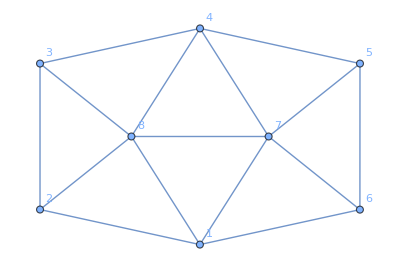
```mathematica
(* Output is list of vertices as {1,2,3,4,5,6,7,8} in -Graphics-. *)
detectnonisohexagonwithtwovertsinmiddle[fgraph_]:=Module[{alldts,dtscurrent,dtsnoniso,autos,orderedverts},alldts=FindIsomorphicSubgraph[(fgraph//displayfgraph)[[1,1]],-Graphics-,All];
autos=graphAutomorphisms[fgraph];
dtscurrent=alldts;
dtsnoniso={};
While[Length[dtscurrent]>0,dtsnoniso=Append[dtsnoniso,dtscurrent[[1]]];dtscurrent=Complement[dtscurrent,Table[VertexReplace[dtscurrent[[1]],ii],{ii,autos}],SameTest->IGSameGraphQ  ]];
(Range[8]/.(FindGraphIsomorphism[-Graphics-,#][[1]]/.Association->List))&/@dtsnoniso]
```

```mathematica
sidewaysbinaryrulegenerate[fg_]:=Module[{dts,newfgs},
dts=detectnonisohexagonwithtwovertsinmiddle[fg];
(* Delete cases with a numerator between 4 and 1 *)
dts=Select[dts,0=!=(fg/.{x[#[[1]],#[[4]]]:>0,x[#[[4]],#[[1]]]:>0})&];
newfgs=If[dts==={},{},(fg*(Numerator[fg]/.x[a_,b_]:>x[a/.{#[[7]]->#[[8]],#[[8]]->#[[7]]},b/.{#[[7]]->#[[8]],#[[8]]->#[[7]]}])/Numerator[fg]/.x[a_,b_]:>x[b,a]/;(a>b))&/@dts];
canonicalizefgraph/@newfgs]
```

```mathematica
fGraphList[4][[1]]
amplitudeCoefficients[4][[1]]
sidewaysbinaryrulegenerate[fGraphList[4][[1]]]
Position[fGraphListcan[4],#][[1,1]]&/@%
amplitudeCoefficients[5][[2]]
```

(x[5,6] x[7,8])/(x[1,4] x[1,6] x[1,7] x[1,8] x[2,3] x[2,5] x[2,6] x[2,8] x[3,5] x[3,6] x[3,7] x[4,5] x[4,7] x[4,8] x[5,7] x[5,8] x[6,7] x[6,8])

1

{1/(x[1,2] x[1,3] x[1,4] x[1,6] x[2,3] x[2,5] x[2,7] x[3,6] x[3,7] x[4,5] x[4,6] x[4,8] x[5,7] x[5,8] x[6,8] x[7,8])}

{2}

-1

```mathematica
nn=3;
rrgen=rungrulegenerate[#]&/@fGraphListcan[nn];
rrgennum=(Position[fGraphListcan[nn+1],#][[1,1]]&/@#)&/@rrgen;
If[(((Union[amplitudeCoefficients[nn+1][[#]]&/@#])&/@rrgennum)===
(List/@amplitudeCoefficients[nn])),Print[nn, " loop to ",nn+1," loop rung rule coefficients all agree"]]
rrgennum2=rrgennum//Flatten//Union;
Print["List of rungrule generated graphs at ",nn+1," loops:",rrgennum2]
rrgenlist=fGraphListcan[nn+1][[#]]&/@rrgennum2;
sidewaysgen=sidewaysbinaryrulegenerate[#]&/@rrgenlist;
sidewaysgennum=(Position[fGraphListcan[nn+1],#][[1,1]]&/@#)&/@sidewaysgen;
coeftest=Table[(amplitudeCoefficients[nn+1][[rrgennum2[[kkk]]]]==-amplitudeCoefficients[nn+1][[#]])&/@(sidewaysgennum[[kkk]]),{kkk,Length[rrgenlist]}]//Flatten//Union;
If[coeftest==={True},Print[nn+1, " loop sideways coefficients are all correctly -1 related"]]
Print["List of sideways generated graphs at ",nn+1," loops:",Union[Flatten[sidewaysgennum]]]
Print["Total number of generated graphs at ",nn+1," loops:",Length[Union[Flatten[{rrgennum2,sidewaysgennum}]]], " out of a total: ", Length[amplitudeCoefficients[nn+1]]]

Clear[nn,rrgen,rrgennum,rrgenlist,sidewaysgen,sidewaysgennum,coeftest]
```

3 loop to 4 loop rung rule coefficients all agree

List of rungrule generated graphs at 4 loops:{1,3}

4 loop sideways coefficients are all correctly -1 related

List of sideways generated graphs at 4 loops:{2}

Total number of generated graphs at 4 loops:3 out of a total: 3

```mathematica
nn=4;
rrgen=rungrulegenerate[#]&/@fGraphListcan[nn];
rrgennum=(Position[fGraphListcan[nn+1],#][[1,1]]&/@#)&/@rrgen;
If[(((Union[amplitudeCoefficients[nn+1][[#]]&/@#])&/@rrgennum)===
(List/@amplitudeCoefficients[nn])),Print[nn, " loop to ",nn+1," loop rung rule coefficients all agree"]]
rrgennum2=rrgennum//Flatten//Union;
Print["List of rungrule generated graphs at ",nn+1," loops:",rrgennum2]
rrgenlist=fGraphListcan[nn+1][[#]]&/@rrgennum2;
sidewaysgen=sidewaysbinaryrulegenerate[#]&/@rrgenlist;
sidewaysgennum=(Position[fGraphListcan[nn+1],#][[1,1]]&/@#)&/@sidewaysgen;
coeftest=Table[(amplitudeCoefficients[nn+1][[rrgennum2[[kkk]]]]==-amplitudeCoefficients[nn+1][[#]])&/@(sidewaysgennum[[kkk]]),{kkk,Length[rrgenlist]}]//Flatten//Union;
If[coeftest==={True},Print[nn+1, " loop sideways coefficients are all correctly -1 related"]]
Print["List of sideways generated graphs at ",nn+1," loops:",Union[Flatten[sidewaysgennum]]]
Print["Total number of generated graphs at ",nn+1," loops:",Length[Union[Flatten[{rrgennum2,sidewaysgennum}]]], " out of a total: ", Length[amplitudeCoefficients[nn+1]]]

Clear[nn,rrgen,rrgennum,rrgenlist,sidewaysgen,sidewaysgennum,coeftest]
```

4 loop to 5 loop rung rule coefficients all agree

List of rungrule generated graphs at 5 loops:{1,3,4,5,6}

5 loop sideways coefficients are all correctly -1 related

List of sideways generated graphs at 5 loops:{2,5}

Total number of generated graphs at 5 loops:6 out of a total: 7

```mathematica
nn=5;
rrgen=rungrulegenerate[#]&/@fGraphListcan[nn];
rrgennum=(Position[fGraphListcan[nn+1],#][[1,1]]&/@#)&/@rrgen;
If[(((Union[amplitudeCoefficients[nn+1][[#]]&/@#])&/@rrgennum)===
(List/@amplitudeCoefficients[nn])),Print[nn, " loop to ",nn+1," loop rung rule coefficients all agree"]]
rrgennum2=rrgennum//Flatten//Union;
Print["List of rungrule generated graphs at ",nn+1," loops:",rrgennum2]
rrgenlist=fGraphListcan[nn+1][[#]]&/@rrgennum2;
sidewaysgen=sidewaysbinaryrulegenerate[#]&/@rrgenlist;
sidewaysgennum=(Position[fGraphListcan[nn+1],#][[1,1]]&/@#)&/@sidewaysgen;
coeftest=Table[(amplitudeCoefficients[nn+1][[rrgennum2[[kkk]]]]==-amplitudeCoefficients[nn+1][[#]])&/@(sidewaysgennum[[kkk]]),{kkk,Length[rrgenlist]}]//Flatten//Union;
If[coeftest==={True},Print[nn+1, " loop sideways coefficients are all correctly -1 related"]]
Print["List of sideways generated graphs at ",nn+1," loops:",Union[Flatten[sidewaysgennum]]]
Print["Total number of generated graphs at ",nn+1," loops:",Length[Union[Flatten[{rrgennum2,sidewaysgennum}]]], " out of a total: ", Length[amplitudeCoefficients[nn+1]]]

Clear[nn,rrgen,rrgennum,rrgenlist,sidewaysgen,sidewaysgennum,coeftest]
```

5 loop to 6 loop rung rule coefficients all agree

List of rungrule generated graphs at 6 loops:{2,4,5,6,7,8,9,11,12,13,15,17,19,21,24,25,27,28,29,30,32}

6 loop sideways coefficients are all correctly -1 related

List of sideways generated graphs at 6 loops:{3,5,7,13,15,17,18,25,28,31,32,34}

Total number of generated graphs at 6 loops:25 out of a total: 36

```mathematica
nn=7;
rrgen=rungrulegenerate[#]&/@fGraphListcan[nn];
rrgennum=(Position[fGraphListcan[nn+1],#][[1,1]]&/@#)&/@rrgen;
If[(((Union[amplitudeCoefficients[nn+1][[#]]&/@#])&/@rrgennum)===
(List/@amplitudeCoefficients[nn])),Print[nn, " loop to ",nn+1," loop rung rule coefficients all agree"]]
rrgennum2=rrgennum//Flatten//Union;
Print["List of rungrule generated graphs at ",nn+1," loops:",rrgennum2]
rrgenlist=fGraphListcan[nn+1][[#]]&/@rrgennum2;
sidewaysgen=sidewaysbinaryrulegenerate[#]&/@rrgenlist;
sidewaysgennum=(Position[fGraphListcan[nn+1],#][[1,1]]&/@#)&/@sidewaysgen;
coeftest=Table[(amplitudeCoefficients[nn+1][[rrgennum2[[kkk]]]]==-amplitudeCoefficients[nn+1][[#]])&/@(sidewaysgennum[[kkk]]),{kkk,Length[rrgenlist]}]//Flatten//Union;
If[coeftest==={True},Print[nn+1, " loop sideways coefficients are all correctly -1 related"]]
Print["List of sideways generated graphs at ",nn+1," loops:",Union[Flatten[sidewaysgennum]]]
Print["Total number of generated graphs at ",nn+1," loops:",Length[Union[Flatten[{rrgennum2,sidewaysgennum}]]], " out of a total: ", Length[amplitudeCoefficients[nn+1]]]

Clear[nn,rrgen,rrgennum,rrgenlist,sidewaysgen,sidewaysgennum,coeftest]
```

7 loop to 8 loop rung rule coefficients all agree

List of rungrule generated graphs at 8 loops:{1,2,4,5,6,8,11,12,13,14,15,16,17,18,50,51,52,53,54,55,56,57,58,59,60,63,64,65,66,67,68,69,73,74,77,78,79,80,81,83,85,88,89,90,91,92,93,96,99,100,101,102,107,108,109,110,111,112,113,114,115,118,119,120,124,125,126,128,129,130,131,132,133,134,135,136,137,139,140,141,142,143,144,145,146,147,148,149,150,151,154,155,156,157,158,159,160,164,167,168,169,170,171,172,173,174,175,180,184,187,188,189,190,192,194,195,196,201,202,203,204,207,209,210,211,212,213,214,215,216,217,218,219,220,221,222,223,225,226,227,228,229,230,231,232,234,235,236,238,241,242,244,247,248,249,253,254,255,256,257,258,262,265,266,267,268,269,270,271,272,274,275,276,277,278,279,280,281,282,283,284,285,286,287,288,289,290,291,292,293,294,295,296,297,298,299,300,301,302,303,304,305,306,307,308,309,311,312,313,314,315,316,317,318,319,320,321,323,324,325,326,327,328,329,330,331,332,333,334,335,336,337,338,339,340,341,342,343,344,345,346,347,348,349,350,352,353,354,355,356,357,358,359,360,361,362,364,365,366,368,370,371,373,374,375,376,377,378,379,380,381,382,383,384,385,386,387,390,391,393,394,395,396,397,398,399,400,402,403,404,406,409,410,411,413,415,416,417,418,420,423,425,426,427,428,431,432,433,434,435,436,437,438,439,442,443,446,447,448,449,451,452,455,456,458,459,460,461,462,463,466,467,468,469,470,472,473,474,475,476,477,478,479,481,482,483,487,488,489,490,497,498,499,501,502,503,507,508,509,510,511,512,513,514,515,519,520,521,527,529,530,531,532,538,539,544,546,547,551,552,553,555,558,560,562,563,564,565,566,567,568,574,575,576,577,578,580,590,591,592,596,597,598,599,602,603,604,606,608,609,610,611,612,613,614,615,616,617,618,619,622,623,624,625,633,634,637,640,644,646,649,651,654,656,661,662,664,665,666,667,668,669,670,671,673,674,675,676,677,678,679,680,681,682,683,684,685,686,688,689,690,693,694,695,696,697,698,699,700,701,702,703,704,705,707,708,709,710,711,712,713,714,715,716,717,718,719,720,721,722,723,724,725,726,727,730,731,733,734,736,738,739,740,742,745,747,756,758,759,761,763,764,765,766,767,769,770,771,772,774,775,778,780,781,782,785,786,787,788,789,790,791,794,795,797,798,799,800,801,803,804,806,807,810,812,813,814,817,819,821,823,824,825,826,827,828,829,830,831,832,833,834,835,836,837,849,851,852,853,855,858,859,862,863,864,865,866,867,868,869,882,883,894,896,897,899,900,901,902,904,906,907,908,909,910,913,914,916,919,920,921,925,930,931,941,942,943,944,945,946,947,948,949,950,951,953,954,955,957,958,960,961,962,967,968,969,970,971,972,973,975,976,977,981,982,983,984,985,986,987,988,991,993,995,998,999,1002,1003,1004,1005,1006,1007,1008,1009,1014,1015,1016,1019,1020,1021,1022,1024,1025,1026,1028,1030,1031,1033,1034,1037,1040,1042,1048,1050,1051,1054,1055,1056,1057,1058,1059,1060,1064,1065,1066,1069,1070,1071,1073,1077,1078,1080,1084,1087,1090,1092,1093,1095,1096,1097,1100,1101,1104,1105,1120,1122,1123,1125,1127,1128,1129,1130,1131,1132,1133,1134,1135,1136,1137,1140,1141,1142,1143,1153,1154,1156,1157,1158,1159,1160,1161,1162,1163,1164,1166,1168,1169,1170,1171,1172,1173,1175,1176,1177,1179,1180,1181,1182,1188,1189,1193,1195,1197,1203,1204,1205,1206,1208,1209,1210,1211,1218,1222,1223,1225,1227,1228,1232,1240,1241,1242,1244,1245,1247,1248,1249,1251,1253,1254,1256,1257,1259,1262,1265,1268,1269,1271,1272,1274,1275,1276,1277,1279,1281,1284,1285,1286,1289,1290,1292,1294,1296,1297,1299,1300,1301,1304,1307,1308,1313,1315,1316,1317,1318,1319,1320,1321,1322,1323,1325,1326,1328,1329,1330,1331,1341,1342,1343,1345,1346,1350,1353,1354,1355,1356,1357,1358,1359,1360,1361,1362,1363,1368,1370,1371,1372,1373,1376,1377,1378,1381,1383,1384,1385,1386,1388,1389,1390,1393,1395,1396,1397,1398,1399,1400,1401,1402,1403,1404,1405,1406,1407,1408,1409,1410,1411,1414,1415,1416,1417,1419,1420,1421,1422,1423,1425,1429,1430,1432,1433,1434,1435,1436,1437,1444,1445,1446,1447,1449,1450,1451,1452,1453,1454,1462,1463,1464,1465,1467,1468,1469,1470,1471,1472,1473,1476,1477,1483,1486,1488,1490,1491,1492,1493,1494,1495,1496,1497,1498,1500,1501,1502,1503,1504,1505,1506,1507,1508,1509,1510,1511,1512,1514,1515,1516,1517,1522,1526,1528,1529,1532,1533,1536,1537,1538,1540,1541,1542,1543,1545,1546,1547,1548,1549,1551,1553,1554,1555,1557,1558,1561,1564,1565,1566,1567,1570,1571,1573,1574,1575,1577,1578,1580,1582,1583,1584,1585,1586,1587,1588,1589,1590,1591,1592,1593,1594,1597,1600,1601,1602,1603,1604,1605,1606,1610,1611,1612,1613,1614,1615,1616,1617,1618,1619,1620,1621,1622,1623,1625,1626,1627,1628,1629,1630,1631,1632,1633,1634,1635,1636,1637,1638,1639,1640,1641,1642,1643,1645,1647,1648,1649,1651,1652,1653,1654,1655,1656,1657,1658,1659,1661,1662,1665,1668,1669,1671,1672,1673,1674,1675,1676,1677,1678,1679,1680,1681,1682,1683,1684,1685,1686,1687,1688,1689,1690,1693,1694,1695,1697,1698,1700,1702,1703,1704,1705,1706,1707,1708,1709,1710,1711,1712,1713,1714,1715,1717,1718,1720,1721,1722,1723,1724,1725,1726,1727,1728,1729,1731,1732,1733,1737,1740,1743,1744,1745,1746,1747,1751,1752,1753,1755,1756,1758,1759,1760,1762,1763,1764,1765,1766,1767,1768,1769,1771,1774,1775,1776,1777,1778,1779,1780,1781,1782,1783,1784,1785,1786,1787,1788,1789,1790,1791,1792,1793,1794,1795,1796,1797,1798,1799,1800,1801,1802,1803,1804,1807,1808,1810,1811,1812,1813,1814,1815,1816,1817,1818,1819,1820,1823,1824,1825,1826,1827,1830,1832,1833,1834,1837,1838,1839,1840,1841,1842,1844,1845,1846,1848,1849,1850,1851,1853,1854,1855,1856,1860,1861,1864,1865,1866,1867,1868,1869,1870,1871,1875,1876,1877,1878,1879,1880,1881,1882,1883,1884,1885,1886,1893,1896,1897,1899,1900,1901,1902,1903,1904,1905,1906,1908,1909,1910,1913,1914,1915,1916,1919,1920,1926,1929,1931,1934,1935,1940,1942,1943,1944,1947,1948,1951,1952,1955,1958,1962,1963,1965,1966,1968,1970,1975,1977,1979,1980,1984,1988,1989,1990,1991,1992,1993,1995,1996,1997,1998,2002,2004,2006,2007,2009,2011,2014,2015,2016,2017,2018,2019,2022,2023,2024,2025,2026,2027,2029,2031,2032,2033,2034,2035,2036,2038,2039,2040,2043,2044,2045,2046,2047,2048,2049,2052,2053,2054,2055,2056,2057,2058,2060,2061,2062,2063,2064,2065,2066,2067,2068,2071,2072,2074,2075,2076,2077,2081,2082,2085,2086,2087,2088,2089,2090,2091,2094,2095,2096,2097,2100,2102,2104,2105,2110,2111,2112,2113,2114,2116,2117,2121,2126,2131,2132,2133,2134,2137,2138,2141,2142,2143,2144,2145,2146,2148,2149,2152,2153,2155,2157,2158,2160,2161,2162,2165,2167,2168,2171,2172,2173,2176,2177,2178,2180,2181,2182,2183,2185,2186,2187,2189,2190,2191,2192,2193,2194,2195,2196,2197,2198,2199,2200,2201,2202,2203,2206,2207,2208,2209,2210,2211,2212,2213,2214,2216,2218,2219,2221,2222,2225,2226,2227,2228,2231,2232,2233,2237,2242,2244,2245,2246,2247,2249,2255,2257,2262,2267,2269,2272,2274,2277,2283,2284,2285,2286,2287,2290,2291,2292,2293,2294,2295,2296,2298,2299,2300,2301,2302,2304,2305,2306,2307,2309,2310,2311,2312,2315,2316,2318,2320,2321,2322,2324,2326,2328,2329,2331,2336,2338,2340,2342,2344,2349,2352,2354,2355,2357,2358,2361,2363,2364,2365,2366,2369,2373,2375,2378,2381,2383,2384,2385,2388,2389,2391,2393,2394,2395,2397,2400,2401,2403,2405,2406,2407,2408,2409,2410,2411,2412,2413,2414,2415,2419,2420,2421,2422,2425,2426,2427,2430,2434,2435,2437,2439,2440,2443,2444,2445,2446,2447,2451,2452,2453,2457,2458,2460,2461,2468,2469,2470,2471,2472,2475,2476,2477,2478,2481,2483,2484,2485,2487,2489,2492,2494,2498,2500,2501,2507,2508,2509,2510,2515,2520,2523,2527,2534,2536,2539,2547,2550,2551,2552,2555,2556,2558,2559,2565,2566,2567,2569,2570,2571,2572,2573,2580,2582,2583,2584,2586,2587,2588,2591,2593,2595,2596,2600,2601,2603,2604,2605,2606,2607,2608,2610,2614,2616,2617,2620,2621,2625,2627,2630,2634,2635,2637,2638,2643,2644,2647,2648,2649,2652,2654,2655,2658,2662,2664,2666,2673,2675,2676,2677,2679,2685,2690,2691,2694,2696}

8 loop sideways coefficients are all correctly -1 related

List of sideways generated graphs at 8 loops:{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,50,51,52,54,55,56,57,60,61,63,65,66,68,69,71,72,73,74,77,78,79,80,81,82,83,84,85,86,89,90,91,93,94,96,97,99,100,101,102,104,105,107,108,114,115,118,119,120,123,124,125,126,129,130,133,136,139,142,143,144,146,150,151,160,192,194,195,199,201,202,207,209,210,211,212,213,214,215,216,219,221,222,223,225,226,227,228,229,230,234,235,238,242,243,244,247,248,250,251,253,255,256,257,258,259,260,262,266,268,271,272,276,277,278,280,281,282,285,293,294,295,296,297,298,299,300,303,307,311,312,313,314,316,317,318,320,321,322,323,325,328,337,338,339,340,341,343,345,349,350,352,359,360,362,365,370,371,376,377,378,379,380,382,384,385,387,389,390,391,393,400,413,414,418,419,420,423,426,431,432,433,434,435,436,437,438,439,440,463,466,467,468,469,470,477,478,482,487,489,490,492,493,498,500,501,507,508,509,510,511,512,513,515,516,517,518,519,520,524,530,531,532,537,553,568,570,572,573,574,579,580,581,582,584,585,588,590,591,592,593,596,597,598,600,603,604,605,606,607,608,613,614,615,616,618,619,620,622,623,624,625,626,637,641,644,646,654,659,662,666,670,674,680,681,685,702,703,704,705,706,707,708,709,711,712,714,716,717,718,720,722,723,725,727,729,730,731,732,733,734,735,736,738,739,740,742,745,746,747,750,756,757,758,759,761,762,763,764,765,766,770,771,772,773,774,775,776,777,780,781,782,783,784,785,786,788,789,790,791,793,794,795,796,801,803,806,807,809,812,819,820,823,824,825,826,827,833,834,836,837,839,840,845,849,851,852,854,855,856,858,862,863,864,865,866,867,868,869,870,882,883,884,894,896,897,898,899,900,902,903,908,909,910,913,922,930,931,932,941,942,944,945,950,951,958,960,961,969,970,983,984,985,986,987,988,990,991,992,993,995,997,998,999,1004,1006,1007,1008,1009,1010,1011,1014,1016,1017,1021,1040,1050,1051,1052,1053,1054,1055,1056,1057,1058,1059,1060,1061,1062,1063,1064,1065,1066,1067,1068,1069,1070,1071,1073,1077,1078,1081,1083,1085,1088,1089,1090,1091,1092,1093,1094,1095,1096,1097,1098,1100,1101,1102,1103,1104,1105,1108,1109,1112,1113,1114,1120,1121,1122,1123,1124,1125,1126,1127,1128,1129,1132,1133,1134,1135,1136,1138,1139,1140,1141,1142,1143,1144,1146,1147,1150,1151,1152,1153,1154,1155,1156,1157,1158,1159,1161,1162,1163,1164,1166,1167,1175,1177,1180,1181,1182,1183,1184,1185,1186,1187,1189,1193,1194,1195,1197,1202,1203,1206,1207,1208,1209,1210,1211,1217,1218,1219,1220,1223,1224,1225,1227,1228,1231,1235,1237,1240,1244,1245,1247,1254,1257,1275,1276,1281,1284,1289,1290,1291,1292,1296,1298,1299,1300,1301,1302,1303,1307,1312,1313,1314,1315,1317,1318,1319,1325,1326,1327,1328,1329,1330,1331,1341,1345,1346,1347,1350,1352,1353,1354,1355,1356,1357,1358,1359,1360,1362,1363,1366,1367,1370,1372,1376,1378,1383,1384,1385,1386,1388,1389,1390,1391,1393,1395,1397,1398,1399,1400,1401,1402,1403,1406,1408,1409,1410,1414,1415,1416,1417,1418,1419,1420,1421,1422,1423,1424,1425,1429,1430,1433,1434,1435,1436,1437,1438,1440,1442,1444,1446,1454,1471,1472,1473,1474,1476,1477,1478,1500,1501,1502,1503,1504,1505,1506,1507,1508,1509,1511,1514,1515,1517,1528,1529,1537,1538,1548,1549,1553,1555,1558,1565,1584,1585,1586,1587,1588,1591,1592,1593,1594,1596,1597,1598,1599,1600,1601,1602,1603,1606,1610,1611,1612,1613,1620,1621,1622,1624,1625,1626,1627,1628,1629,1632,1633,1634,1635,1642,1649,1654,1655,1656,1657,1662,1669,1671,1672,1673,1675,1676,1677,1678,1679,1680,1682,1683,1695,1698,1706,1707,1708,1709,1711,1712,1724,1725,1728,1729,1731,1732,1733,1734,1735,1737,1738,1741,1743,1745,1746,1747,1749,1751,1752,1753,1754,1755,1757,1758,1759,1760,1761,1762,1763,1764,1765,1766,1767,1771,1773,1774,1775,1779,1780,1783,1784,1786,1789,1790,1791,1792,1798,1799,1800,1801,1804,1805,1807,1811,1815,1817,1818,1820,1822,1823,1825,1832,1834,1836,1837,1838,1839,1841,1842,1843,1846,1847,1848,1849,1851,1852,1853,1854,1855,1860,1861,1864,1866,1867,1870,1871,1875,1876,1877,1882,1883,1884,1885,1886,1887,1888,1889,1893,1894,1895,1896,1897,1898,1899,1900,1902,1903,1904,1905,1908,1909,1910,1911,1913,1914,1916,1919,1920,1921,1926,1929,1934,1935,1940,1944,1947,1951,1952,1953,1954,1955,1958,1962,1970,1974,1975,1977,1979,1980,1981,1982,1990,1991,1992,1993,1995,1996,1997,1998,1999,2002,2007,2008,2009,2010,2011,2014,2019,2026,2027,2029,2031,2032,2033,2034,2036,2038,2039,2040,2043,2045,2049,2050,2051,2056,2058,2059,2060,2061,2064,2066,2068,2069,2070,2071,2072,2073,2074,2075,2076,2077,2078,2079,2081,2082,2083,2085,2086,2087,2088,2089,2090,2091,2095,2096,2097,2099,2100,2102,2104,2106,2112,2113,2114,2116,2117,2118,2120,2121,2124,2126,2132,2134,2142,2143,2146,2155,2161,2162,2171,2176,2177,2182,2186,2187,2191,2192,2194,2195,2202,2203,2204,2206,2207,2208,2209,2210,2211,2212,2213,2214,2217,2218,2219,2220,2221,2222,2223,2228,2230,2232,2237,2240,2243,2244,2245,2246,2247,2248,2250,2262,2272,2277,2286,2289,2293,2296,2299,2300,2304,2305,2306,2310,2311,2312,2316,2318,2320,2321,2322,2326,2340,2349,2350,2352,2354,2358,2360,2361,2363,2364,2365,2366,2369,2373,2387,2388,2389,2401,2405,2406,2407,2408,2409,2410,2411,2412,2414,2415,2416,2418,2419,2420,2421,2422,2425,2427,2430,2432,2437,2439,2440,2443,2444,2445,2446,2447,2452,2454,2455,2457,2458,2460,2461,2462,2466,2467,2468,2470,2474,2477,2478,2479,2480,2481,2482,2483,2484,2485,2486,2487,2490,2491,2492,2493,2494,2495,2496,2498,2499,2501,2503,2504,2505,2507,2508,2510,2515,2516,2517,2520,2522,2523,2524,2525,2526,2527,2534,2539,2540,2548,2553,2554,2555,2557,2558,2559,2563,2565,2566,2568,2569,2570,2572,2573,2576,2577,2578,2579,2583,2586,2593,2594,2595,2596,2603,2607,2608,2610,2615,2616,2617,2625,2627,2628,2629,2630,2631,2632,2633,2634,2636,2647,2649,2651,2652,2657,2658,2660,2661,2691,2694,2696}

Total number of generated graphs at 8 loops:1928 out of a total: 2709

## L+n loop graphs from L loops (only rung rule)

```mathematica
generateRungWithCoeff[graphsWithCoeff_]:=Module[{rrgen},
rrgen={rungrulegenerate[#[[1]]],#[[2]]}&/@graphsWithCoeff;
DeleteDuplicates[Sequence@@Thread[#]&/@rrgen]
]
```

```mathematica
(*Gives the edges of a graph as String in the notation of the phyton library networkx, that is a list of tuples*)
edgeListNX[edges_List]:=StringReplace[StringReplace[ StringReplace[ToString[edges/. UndirectedEdge->List],{"{"->"(","}"->")"}],{"(("->"[(","))"->")]"}],"()"->"[]"]
```

#### 8 loop from 7 loops

```mathematica
nn=7;
g7loopWithCoeff=Thread[{fGraphListcan[nn],amplitudeCoefficients[nn]}];
```

```mathematica
result8=generateRungWithCoeff[g7loopWithCoeff];
```

```mathematica
result8//Length
```

1661

```mathematica
data={List@@@(List@@Denominator[#[[1]]]),#[[2]]}&/@result8;
```

```mathematica
sameDen=GatherBy[data,First];
```

```mathematica
coefDen=Map[Boole[Or@@#]&,Map[!(#[[2]]===0)&,sameDen,{2}]];
```

```mathematica
denEdges=edgeListNX/@(#[[1,1]]&/@sameDen);
```

```mathematica
dataDen =Transpose[{coefDen,denEdges}];
```

```mathematica
csv=Prepend[dataDen,{"COEFFICIENTS","EDGES"}];
Export["den_graph_data_"<>"7to8"<>".csv",csv]
```

den_graph_data_7to8.csv

#### 8 loop from 7 loops

```mathematica
result9=generateRungWithCoeff[result8];
```

```mathematica
result9//Length
```

13736

```mathematica
data={List@@@(List@@Denominator[#[[1]]]),#[[2]]}&/@result9;
```

```mathematica
sameDen=GatherBy[data,First];
```

```mathematica
coefDen=Map[Boole[Or@@#]&,Map[!(#[[2]]===0)&,sameDen,{2}]];
```

```mathematica
denEdges=edgeListNX/@(#[[1,1]]&/@sameDen);
```

```mathematica
dataDen =Transpose[{coefDen,denEdges}];
```

```mathematica
csv=Prepend[dataDen,{"COEFFICIENTS","EDGES"}];
Export["den_graph_data_"<>"7to9"<>".csv",csv]
```

den_graph_data_7to9.csv

#### 10 loop from 7 loops

```mathematica
result10=generateRungWithCoeff[result9];
```

```mathematica
data={List@@@(List@@Denominator[#[[1]]]),#[[2]]}&/@result10;
```

```mathematica
sameDen=GatherBy[data,First];
```

```mathematica
coefDen=Map[Boole[Or@@#]&,Map[!(#[[2]]===0)&,sameDen,{2}]];
```

```mathematica
denEdges=edgeListNX/@(#[[1,1]]&/@sameDen);
```

```mathematica
dataDen =Transpose[{coefDen,denEdges}];
```

```mathematica
csv=Prepend[dataDen,{"COEFFICIENTS","EDGES"}];
Export["den_graph_data_"<>"7to10"<>".csv",csv]
```

den_graph_data_7to10.csv